# Functions Part 2

## Basic Exercises

### Question Subsection

Use pure functions to define a function that squares a given number.

#### Solution

```mathematica
square = #^2&
```

#1^2&

```mathematica
square[3]
```

9

### Question Subsection

Use pure functions to define a function that raises a given number to any given number.

#### Hint

You can provide multiple arguments to pure functions using #1, #2, #3, #4, ...

```mathematica
?Slot
```

# represents the first argument supplied to a pure function. 
StyleBox[RowBox[{"#", StyleBox["n", "TI"]}]] represents the StyleBox[RowBox[{StyleBox["n", "TI"], ""}]]SuperscriptBox["", "th"] argument. 
StyleBox[RowBox[{"#", StyleBox["name", "TI"]}]] represents the value associated with key "
StyleBox["name", "TI"]" in an association in the first argument.

#### Solution

```mathematica
power=#1^#2&
```

#1^#2&

```mathematica
power[2,4]
```

16

### Question Subsection

Write a pure function that given a coordinate point {x, y}, computes its distance from the origin.

#### Solution

```mathematica
dist=Sqrt[#1^2+#2^2]&
```

√(#1^2+#2^2)&

```mathematica
dist[2,3]
```

√13

### Question Subsection

Write a pure function that returns True, if the input is an integer, and False otherwise.

#### Solution

```mathematica
MatchQ[#,_Integer]&[3]
```

True

or

```mathematica
IntegerQ[#]&[3]
```

True

### Question Subsection

Write a pure function that takes any number of arguments (not in a list) and returns their sum.

#### Hint

You can use ## to represent sequence of arguments.

#### Solution

```mathematica
Total[{##}]&[1,2,3]
```

6

## Intermediate Exercises

### Question Subsection

Given the following list of lists, use Select and pure functions to pick out the sublists whose total sum is greater than 10.

```mathematica
list = Table[RandomInteger[5,3],10]
```

{{5,3,5},{4,3,1},{1,1,5},{2,1,0},{3,5,5},{1,0,2},{5,2,2},{4,5,1},{1,4,0},{4,5,1}}

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

#### Solution

```mathematica
Select[list,Total[#]>10&]
```

{{5,3,5},{3,5,5}}

### Question Subsection

use Map and pure functions to produce a list containing the following graphics object rotated by the amount specified in rlist.

```mathematica
g=Graphics[{RGBColor[0.6,0.8,0.8],Rectangle[]},ImageSize->20]
```

-Graphics-

```mathematica
rlist=RandomReal[2*Pi,10]
```

{4.47811,3.2273,3.80311,3.15956,0.202531,5.34936,1.71075,0.801506,0.98623,5.04064}

#### Solution

```mathematica
Map[Rotate[g,#]&,rlist]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Question Subsection

Given the following list of integers, use MapIndexed and pure functions to highlight those numbers that are in odd positions with a yellow background.

```mathematica
list = RandomInteger[10,10]
```

{6,6,0,6,3,1,9,6,0,8}

#### Hint

Look at conditionals.

#### Solution

```mathematica
MapIndexed[If[OddQ[#2[[1]]],Framed[#1,Background->Yellow],#1]&,list]
```

{6,6,0,6,3,1,9,6,0,8}

## Advanced Exercises

### Question Subsection

Given a list of coordinate points {x,y} where 0 < x, y <1, create a list of Disk[]s whose colors are RGBColor[x, y, position of the point in the list normalized to be between 0 and 1]. Plot these points. Plot these Disk[]s.

```mathematica
coords = Table[{RandomReal[1],RandomReal[1]},5000];
```

#### Solution

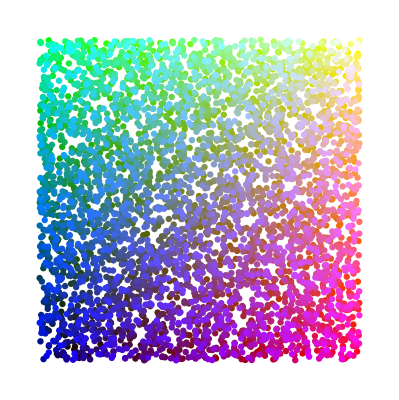

```mathematica
Graphics[MapIndexed[{RGBColor[#1[[1]],#1[[2]],#2[[1]]/Length[coords]],Disk[#1,0.01]}&,coords]]
```

### Question Subsection

Given a list of n coordinate points {x,y} and a list of n values z below, plot these points in 3D space as spheres at {x,y, normalized z}, and make the color of these points to be RGBColor[normalized z, 0, 1 - normalized z]

Note: generally this is not an ideal way of plotting mathematical functions. You will notice the resulting graphics consumes a lot of resources. If you want to avoid that, you can use ListPlot3D to render the graphics instead of plotting spheres.

```mathematica
coords = Table[{RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}]},5000];
zs = coords/.{{x_,y_}:> Sin[x y]};
```

#### Solution

```mathematica
Graphics3D[MapThread[{RGBColor[#2/Max[zs],0,1-#2/Max[zs]],Sphere[{#1[[1]],#1[[2]],#2/Max[zs]},0.1]}&,{coords,zs}],ImageSize->Large]
```

-Graphics3D-

Or

```mathematica
ListPlot3D[MapThread[{#1[[1]],#1[[2]],#2}&,{coords,zs}],ImageSize->Large,ColorFunction->"SouthwestColors"]
```

-Graphics3D-